```mathematica
(* find evolution operator *)

Clear[ψ];
ψ0 = {1, 0, 0, 0, 0, 0, 0, 0};
funcs=Array[ψ[#2 + Length[ψ0]*(#1- 1)][t]&,{Length[ψ0],Length[ψ0]}];

equations=Flatten@Join[Thread[Mtrans.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[Length[ψ0]]/.t->0]];

eOperator= NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]];
```

```mathematica
eOperator /. t->Tmax // Chop // MatrixForm;
eOperator.ConjugateTranspose[eOperator] /. t-> Tmax // Chop // MatrixForm;
(*Inverse[(eOperator /. t->1*10^-7)].(eOperator /. t->(T + 1*10^-7)) // Chop // MatrixForm;*)

Tstart = 0
Tend = Tmax

M = (((eOperator /. t->(Tend)).ConjugateTranspose[(eOperator /. t->Tstart)])[[{1, 2}, {1, 2}]]);
M // MatrixForm

"ROTATING BASIS CHANGE"
Utarget = Cos[θ]*σX + Sin[θ]*σY;

F = (1/6)Sum[.25*Tr[Utarget.(σI + σi).ConjugateTranspose[Utarget].M.(σI + σi).ConjugateTranspose[M]], {σi, {σX, -σX, σY, -σY, σZ, -σZ}}];

NMaximize[Abs[F], {θ}]
th = θ/.NMaximize[Abs[F], {θ}][[2]]

eOperatorTransformed = DiagonalMatrix[{1, E^(-ⅈ*2*th*((t - Tstart)/Tend)), 1, 1, 1, 1, 1, 1}].eOperator;
M = (((eOperatorTransformed /. t->(Tend)).ConjugateTranspose[(eOperatorTransformed /. t->Tstart)])[[{1, 2}, {1, 2}]]);

(*eOperatorTransformed = (Abs[M[[2]][[1]]]/M[[2]][[1]])^(t/T)*eOperatorTransformed;
M = (((eOperatorTransformed /. t->(T + 1*10^-7)).ConjugateTranspose[(eOperatorTransformed /. t->1*10^-7)])[[{1, 2}, {1, 2}]]);
*)
M // Chop // MatrixForm
Utarget = σX;
F = (1/6)Sum[.25*Tr[Utarget.(σI + σi).ConjugateTranspose[Utarget].M.(σI + σi).ConjugateTranspose[M]], {σi, {σX, -σX, σY, -σY, σZ, -σZ}}];

F

"STATIC BASIS CHANGE"
Clear[α, β];
eOperatorTransformed = DiagonalMatrix[{E^(ⅈ*α), E^(ⅈ*β), 1, 1, 1, 1, 1, 1}].eOperator.DiagonalMatrix[{E^(-ⅈ*α), E^(-ⅈ*β), 1, 1, 1, 1, 1, 1}];
M = (((eOperatorTransformed /. t->(Tend)).ConjugateTranspose[(eOperatorTransformed /. t->Tstart)])[[{1, 2}, {1, 2}]]);

M // MatrixForm

Utarget = σX;
F = (1/6)Sum[.25*Tr[Utarget.(σI + σi).ConjugateTranspose[Utarget].M.(σI + σi).ConjugateTranspose[M]], {σi, {σX, -σX, σY, -σY, σZ, -σZ}}] // FullSimplify // Chop;

NMaximize[F, {α, β}]
```

0

1/10000000

Part::partd: Part specification (eOperator.ConjugateTranspose[eOperator])⟦{1,2},{1,2}⟧ is longer than depth of object.

(eOperator.ConjugateTranspose[eOperator])⟦{1,2},{1,2}⟧

ROTATING BASIS CHANGE

Part::partd: Part specification (eOperator.ConjugateTranspose[eOperator])⟦{1,2},{1,2}⟧ is longer than depth of object.

NMaximize::nnum: The function value -1/6 Abs[0.25 Tr[{{0,0},{0,2.}}.(eOperator.ConjugateTranspose[«1»])⟦{1,2},{1,2}⟧.{{2,0},{0,0}}.ConjugateTranspose[Dot[«2»]⟦{«2»},{«2»}⟧]]+0.25 Tr[{{1.,-0.996191-0.0871978 ⅈ},{-0.996191+0.0871978 ⅈ,1.}}.(eOperator.ConjugateTranspose[«1»])⟦{1,2},{1,2}⟧.{{1,-ⅈ},{ⅈ,1}}.ConjugateTranspose[Dot[«2»]⟦{«2»},{«2»}⟧]]+0.25 Tr[«1»]+0.25 Tr[«1»]+0.25 Tr[«1»]+0.25 Tr[{{2.,0},{0,0}}.(eOperator.ConjugateTranspose[«1»])⟦{1,2},{1,2}⟧.{{0,0},{0,2}}.ConjugateTranspose[Dot[«2»]⟦{«2»},{«2»}⟧]]] is not a number at {θ} = {-0.829053}.

Part::partd: Part specification (eOperator.ConjugateTranspose[eOperator])⟦{1,2},{1,2}⟧ is longer than depth of object.

NMaximize::nnum: The function value -1/6 Abs[0.25 Tr[{{0,0},{0,2.}}.(eOperator.ConjugateTranspose[«1»])⟦{1,2},{1,2}⟧.{{2,0},{0,0}}.ConjugateTranspose[Dot[«2»]⟦{«2»},{«2»}⟧]]+0.25 Tr[{{1.,-0.996191-0.0871978 ⅈ},{-0.996191+0.0871978 ⅈ,1.}}.(eOperator.ConjugateTranspose[«1»])⟦{1,2},{1,2}⟧.{{1,-ⅈ},{ⅈ,1}}.ConjugateTranspose[Dot[«2»]⟦{«2»},{«2»}⟧]]+0.25 Tr[«1»]+0.25 Tr[«1»]+0.25 Tr[«1»]+0.25 Tr[{{2.,0},{0,0}}.(eOperator.ConjugateTranspose[«1»])⟦{1,2},{1,2}⟧.{{0,0},{0,2}}.ConjugateTranspose[Dot[«2»]⟦{«2»},{«2»}⟧]]] is not a number at {θ} = {-0.829053}.

Part::partd: Part specification (eOperator.ConjugateTranspose[eOperator])⟦{1,2},{1,2}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

Part::partd: Part specification (eOperator.ConjugateTranspose[eOperator])⟦{1,2},{1,2}⟧ is longer than depth of object.

$Aborted

Part::partd: Part specification ({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧ is longer than depth of object.

({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧

1/6 (0.25 Tr[{{0,0},{0,2}}.({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧.{{2,0},{0,0}}.ConjugateTranspose[({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧]]+0.25 Tr[{{1,-1},{-1,1}}.({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧.{{1,-1},{-1,1}}.ConjugateTranspose[({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧]]+0.25 Tr[{{1,-ⅈ},{ⅈ,1}}.({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧.{{1,ⅈ},{-ⅈ,1}}.ConjugateTranspose[({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧]]+0.25 Tr[{{1,ⅈ},{-ⅈ,1}}.({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧.{{1,-ⅈ},{ⅈ,1}}.ConjugateTranspose[({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧]]+0.25 Tr[{{1,1},{1,1}}.({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧.{{1,1},{1,1}}.ConjugateTranspose[({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧]]+0.25 Tr[{{2,0},{0,0}}.({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧.{{0,0},{0,2}}.ConjugateTranspose[({{1,0,0,0,0,0,0,0},{0,ⅇ^(-2 ⅈ th),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.ConjugateTranspose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator])⟦{1,2},{1,2}⟧]])

STATIC BASIS CHANGE

Part::partd: Part specification … is longer than depth of object.

({{ⅇ^(ⅈ α),0,0,0,0,0,0,0},{0,ⅇ^(ⅈ β),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.{{ⅇ^(-ⅈ α),0,0,0,0,0,0,0},{0,ⅇ^(-ⅈ β),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.ConjugateTranspose[{{ⅇ^(ⅈ α),0,0,0,0,0,0,0},{0,ⅇ^(ⅈ β),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}.eOperator.{{ⅇ^(-ⅈ α),0,0,0,0,0,0,0},{0,ⅇ^(-ⅈ β),0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}])⟦{1,2},{1,2}⟧

$Aborted

$Aborted

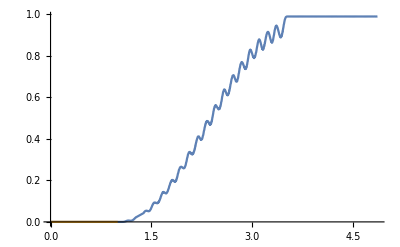

```mathematica
Plot[{Abs[eOperator[[2]][[1]]]^2, state[[2]]}, {t, 0, Tmax}]
```